# Exercise 9

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 9), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex9_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we are going to continue working with boundary conditions for the electric and displacement fields. We are going to look at the behavior of conductors in electric fields, and use the fact that electric field inside a conductor must be zero, which means that, by our boundary conditions for the tangential component of the electric field, our lateral E field at the surface of a conductor must also be zero. You will also have to remember and use Gauss’s Law, which should be good review for the Mid-Term Exam 1.

```mathematica
ClearAll[eps0,eQ, eQxy, efcz, rhofc, rhofctest, eQoriginal, eQmirror, totale, totalexz]
```

## Point Charge Above Conducting Plane

Let’s imagine we place a point charge Q=ϵ_o a distance of h=1m above a grounded conducting plane (at position {0,0,1}).  We know that along the surface, and inside, of the conducting plane, we should have no electric field.  But we also know that our point charge will create an electric field that will extend to the conducting ground plane.  How can this be?  Well, you can think of the free charges in the conducting ground plane rearranging themselves to cancel out the lateral external field.  At the same time, these charges ALSO need to cancel out the vertical field, by assuming a charge density such that no field penetrates into the conductor. Let’s see if we can calculate what the charge distribution will look like on the conducting plane.  
First, let’s figure out what the electric field from our point charge must look like...

```mathematica
eps0=8.85*10^-12;k=1/(4*Pi*eps0);
```

```mathematica
eQ[x_,y_,z_]:=k*eps0*(1/((x^2+y^2+(z-1)^2)^1.5))*{x,y,(z-1)}
```

On the surface of the conductor, the field from the point charge is:

```mathematica
eQxy[x_,y_]:=eQ[x,y,0]
```

The free charge in the conductor have to align in such a way to give a net electric field =0 along the conductor (otherwise, if there was any field in the x or y directions, then charge would move to cancel out this field).  They also must have a charge density strong enough to cancel out the vertical component in the external electric field.  Let’s consider the vertical (z) component of the field

```mathematica
efcz[x_,y_]:=eQxy[x,y][[3]]
```

```mathematica
Plot3D[efcz[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

We can apply boundary conditions to the normal component of the D field, which will consist of our external D field and the field from our free charges.
n̂·((D⃗)^+-(D⃗)^-)=ρ_s, where (D⃗)^+=((D⃗)^+)_ext+ρ_s/2 ϵ_o is the displacement field above the conductor, which comes from the field of the point charge AND the induced surface charge. (D⃗)^- is the displacement inside the conductor, and therefore must be zero.

```mathematica
rhofc[x_,y_]:=2*eps0*efcz[x,y]
```

```mathematica
rhofctest=rhofc[x,y]
```

-(1.40852×10^-12)/((1+x^2+y^2)^1.5)

```mathematica
Plot3D[rhofc[x,y],{x,-2,2},{y,-2,2}, PlotRange->Full]
```

-Graphics3D-

So this gives us a charge distribution on the surface. This charge will create an electric field above the conductor, which we can calculate for any point in space above the conductor, by integrating over the surface charge on the conductor. This integration will be a bit of a (huge) mess. However, there is a much easier way to solve for the electric field in such a system, called the method of images!

## Method of Images

The method of images tells us that if we have a charge distribution above a conducting surface, we can calculate the total field in our system by calculating the field from our original charge distribution AND a virtual charge distribution of opposite sign which is the mirror image of our original charge distribution.  So for the case of a point charge above a conducting plane:

```mathematica
eQoriginal=eQ[x,y,z]
```

{(0.0795775 x)/((x^2+y^2+(-1+z)^2)^1.5),(0.0795775 y)/((x^2+y^2+(-1+z)^2)^1.5),(0.0795775 (-1+z))/((x^2+y^2+(-1+z)^2)^1.5)}

```mathematica
eQmirror=-k*eps0*(1/((x^2+y^2+(z+1)^2)^1.5))*{x,y,(z+1)}
```

{-(0.0795775 x)/((x^2+y^2+(1+z)^2)^1.5),-(0.0795775 y)/((x^2+y^2+(1+z)^2)^1.5),-(0.0795775 (1+z))/((x^2+y^2+(1+z)^2)^1.5)}

```mathematica
totale=Piecewise[{{eQoriginal+eQmirror,z≥0},{{0,0,0},z<0}}]
```

Piecewise[{{{(0.0795775 x)/((x^2+y^2+(-1+z)^2)^1.5)-(0.0795775 x)/((x^2+y^2+(1+z)^2)^1.5),(0.0795775 y)/((x^2+y^2+(-1+z)^2)^1.5)-(0.0795775 y)/((x^2+y^2+(1+z)^2)^1.5),(0.0795775 (-1+z))/((x^2+y^2+(-1+z)^2)^1.5)-(0.0795775 (1+z))/((x^2+y^2+(1+z)^2)^1.5)}, z≥0}, {{0,0,0}, z<0}, {0, True}}]

```mathematica
VectorPlot3D[totale,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

Let’s look at the vector field in the xz plane:

```mathematica
totalexz=Piecewise[{{{(0.07957747154594767 x)/((x^2+(-1+z)^2)^1.5)-(0.07957747154594767 x)/((x^2+(1+z)^2)^1.5),(0.07957747154594767 (-1+z))/((x^2+(-1+z)^2)^1.5)-(0.07957747154594767 (1+z))/((x^2+(1+z)^2)^1.5)}, z≥0}, {{0,0}, z<0}, {0, True}}]
```

Piecewise[{{{(0.0795775 x)/((x^2+(-1+z)^2)^1.5)-(0.0795775 x)/((x^2+(1+z)^2)^1.5),(0.0795775 (-1+z))/((x^2+(-1+z)^2)^1.5)-(0.0795775 (1+z))/((x^2+(1+z)^2)^1.5)}, z≥0}, {{0,0}, z<0}, {0, True}}]

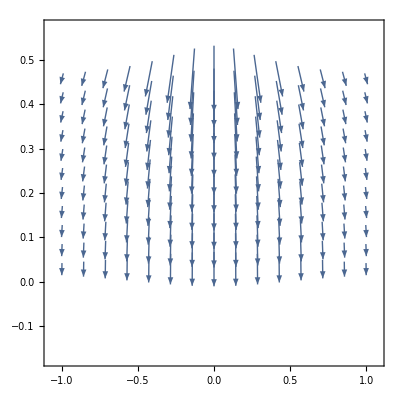

```mathematica
VectorPlot[totalexz,{x,-1,1},{z,-.1,.5}]
```

We see that at the surface of the conducting plane, the lateral electric field is 0.  The electric field is entirely vertical, or in the z-direction.  This makes sense, of course, since the image charge on the opposite side of the conducting plane (with opposite sign) will cancel out the lateral component of the original charge’s field!

## Method of Images (2)

The method of images is a very powerful technique for calculating fields in the vicinity of conducting surfaces.  Now it’s your turn to use this technique!  Calculate the electric field of a charged wire sitting a distance z=2 above a conducting plate held at V=0.  Assume the wire is infinite in the y-direction, and is at x=0.  You can assume whatever linear charge density you like for the line of charge.  Plot the vector field for the system in the xz plane.

We know that the electric field from a linear charge distribution goes as 1/r, where, in this case, r=Sqrt[x^2+(z-2)^2].

```mathematica
ro=TransformedField["Polar"-> "Cartesian",{1/r,0},{r,theta}-> {x,z}]
```

```mathematica
{x/(x^2+z^2),z/(x^2+z^2)}
```

```mathematica
ewire={x/(x^2+(z-2)^2),(z-2)/(x^2+(z-2)^2)}
```

{x/(x^2+(-2+z)^2),(-2+z)/(x^2+(-2+z)^2)}

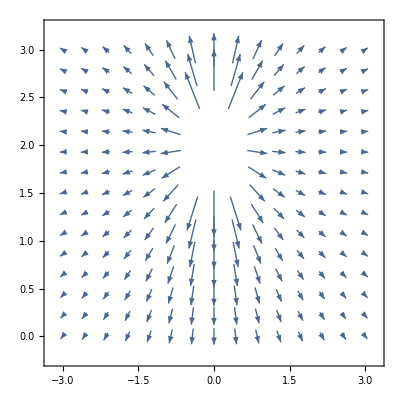

```mathematica
VectorPlot[Boole[x^2+(-2+z)^2>0.5]*ewire,{x,-3,3},{z,0,3}]
```

```mathematica
emirror={-x/(x^2+(z+2)^2),(-(z+2))/(x^2+(z+2)^2)}
```

{-x/(x^2+(2+z)^2),-(2+z)/(x^2+(2+z)^2)}

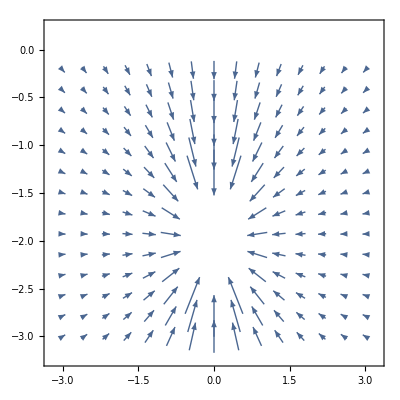

```mathematica
VectorPlot[Boole[x^2+(2+z)^2>0.5]*(emirror),{x,-3,3},{z,0,-3}]
```

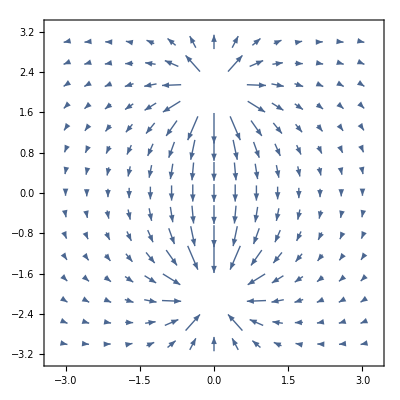

```mathematica
VectorPlot[Boole[x^2+(-2+z)^2>0.5]*Boole[x^2+(2+z)^2>0.5]*(ewire+emirror),{x,-3,3},{z,-3,3}]
```